```mathematica
ps1[x_]:=Style[x,Blue,Bold,18]
```

```mathematica
StyledListLinePlot[x_,y_]:=ListLinePlot[x,PlotStyle->{Red,Orange,Darker[Green],Blue},AxesLabel->{ps1["U,V"],ps1["I,uA"]},LabelStyle->Directive[Blue,Bold,FontSize->18],PlotMarkers->{●,15},GridLines->{Range[-1,1,0.1],Range[0,60,1]},PlotLegends->Placed[Table[ps1[y[[i]]],{i,Length[y]}],Above],ImageSize->Full]
```

```mathematica
StyledListLinePlot[x_]:=StyledListLinePlot[x,{ps1["I"],ps1["I_ionic"]}]
```

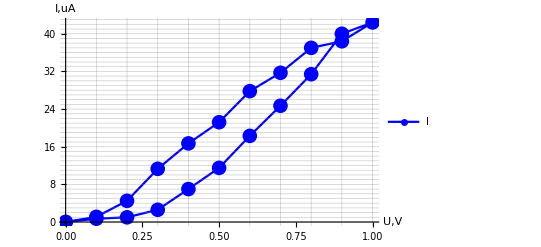

```mathematica
Kz01iv=({{0, 0}, {0.1, .7}, {0.2, 1}, {0.3, 2.6}, {0.4, 7}, {0.5, 11.5}, {0.6, 18.3}, {0.7, 24.7}, {0.8, 31.4}, {0.9, 40}, {1, 42.4}, {0.9, 38.4}, {0.8, 37}, {0.7, 31.7}, {0.6, 27.8}, {0.5, 21.2}, {0.4, 16.7}, {0.3, 11.3}, {0.2, 4.5}, {0.1, 1.1}, {0, 0}});StyledListLinePlot[Kz01iv]
```

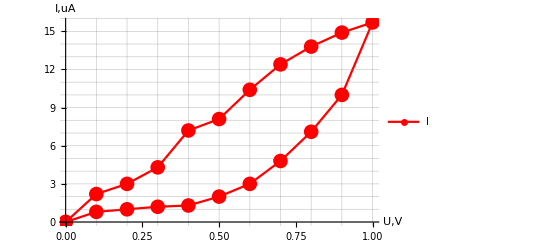

```mathematica
Kz02iv=({{0, 0}, {0.1, .8}, {0.2, 1}, {0.3, 1.2}, {0.4, 1.3}, {0.5, 2}, {0.6, 3}, {0.7, 4.8}, {0.8, 7.1}, {0.9, 10}, {1, 15.7}, {0.9, 14.9}, {0.8, 13.8}, {0.7, 12.4}, {0.6, 10.4}, {0.5, 8.1}, {0.4, 7.2}, {0.3, 4.3}, {0.2, 3}, {0.1, 2.2}, {0, 0}});StyledListLinePlot[{Kz02iv}]
```

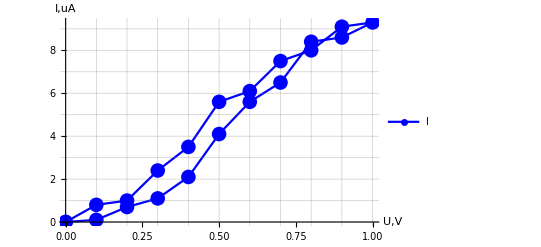

```mathematica
Mz94iv=({{0, 0}, {0.1, .1}, {0.2, .7}, {0.3, 1.1}, {0.4, 2.1}, {0.5, 4.1}, {0.6, 5.6}, {0.7, 6.5}, {0.8, 8.4}, {0.9, 8.6}, {1, 9.3}, {0.9, 9.1}, {0.8, 8}, {0.7, 7.5}, {0.6, 6.1}, {0.5, 5.6}, {0.4, 3.5}, {0.3, 2.4}, {0.2, 1}, {0.1, .8}, {0, 0}});StyledListLinePlot[Mz94iv]
```

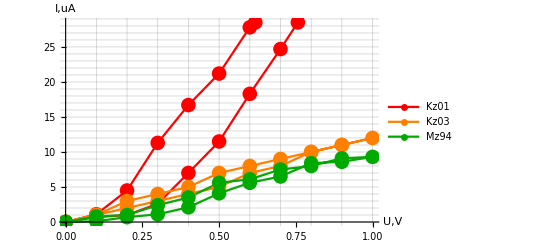

```mathematica
StyledListLinePlot[{Kz01iv,Kz03iv,Mz94iv},{"Kz01","Kz03","Mz94"}]
```